# Chapter 7

## Euler’s Product

## Introduction

```mathematica
Zeta[s]==Product[1/(1-1/Prime[k]^s),{k,1,Infinity}]
```

True

```mathematica
Expand[Integrate[t^(-s),{t,n,n+1},Assumptions->n>0]]
```

-(n^s (n (1+n))^-s)/(-1+s)-(n^(1+s) (n (1+n))^-s)/(-1+s)+(n (1+n)^s (n (1+n))^-s)/(-1+s)

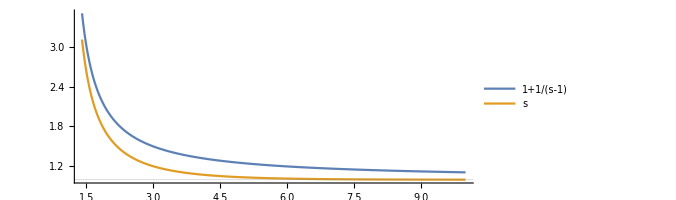

```mathematica
Plot[
{1+1/(s-1),Zeta[s]},
{s,1.4,10},
AxesOrigin->{0,0},
GridLines->{{1},{1}},
PlotRange->All,
PlotLegends->Placed["Expressions",Below],
AspectRatio->Automatic]
```

log(n!)==∑_(p≤n) log(p) Floor[n/p]+∑_(p≤n) log(p) ∑_(j=2)^∞ Floor[n/p^j]

#### Lemma

∑_(p≤n) log(p) ∑_(j=2)^∞ Floor[n/p^j]≪n

#### Proof

∑_(p≤n) log(p) ∑_(j=2)^∞ Floor[n/p^j]<∑_(p≤n) log(p) ∑_(j=2)^∞ n/p^j==n ∑_(p≤n) log(p) ∑_(j=2)^∞ 1/p^j==n ∑_(p≤n) (log(p))/(p^2 (1-1/p))==n ∑_(p≤n) (log(p))/(p (p-1))

This is finite for all primes, not just primes up to n.

```mathematica
Sum[With[{p=Prime[k]},Log[p]/p],{k,1,PrimePi[1000]}]//N
```

5.60951

```mathematica
Log[1000.]
```

6.90776

```mathematica
With[{p=Prime[k]},
Sum[Log[1-1/p]+1/p,{k,1,100000}]]//N
```

-0.315718

```mathematica
1.-Log[2]
```

0.306853

```mathematica
With[{p=Prime[k]},
Sum[Log[1-1/p]+1/p,{k,1,Infinity}]]
```

∑_(k=1)^∞ (Log[1-1/Prime[k]]+1/Prime[k])

```mathematica
1./Exp[EulerGamma]
```

0.561459